```mathematica
Clear["Global`*"]
```

# Quadratures for FEM

## Integrals over elements (triangles)

### Basis

Basis functions for linear space P_1(Δ):={v:v(x,y)=a x+b y+c,(x,y)∈Δ}, Δ:=triangle w/ nodes (x_i,y_i), i∈{1,2,3}

```mathematica
nodes={{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]}};
element=Triangle@nodes;
basisCoef=Inverse@{{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},{Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]},{1,1,1}};
Subscript[ϕ, 1][x_,y_]:=basisCoef[[1]].{x,y,1}
Subscript[ϕ, 2][x_,y_]:=basisCoef[[2]].{x,y,1}
Subscript[ϕ, 3][x_,y_]:=basisCoef[[3]].{x,y,1}
```

```mathematica
K=Triangle[{{0,0},{1,0},{3/4,2}}];
Plot3D[Evaluate[{Subscript[ϕ, 1][x,y],Subscript[ϕ, 2][x,y],Subscript[ϕ, 3][x,y]}/.{Subscript[x, 1]->0,Subscript[y, 1]->0,Subscript[x, 2]->1,Subscript[y, 2]->0,Subscript[x, 3]->3/4,Subscript[y, 3]->2}],{x,y}∈K,PlotRange->{0,1},AxesLabel->{"x","y","z"},PlotLegends->{"ϕ_1","ϕ_2","ϕ_3"},PlotLabel->"Basis functions of P_1(Δ), (x_1,y_1)=(0,0), (x_2,y_2)=(1,0), (x_3,y_3)=(3/4,2)"]
```

-Graphics3D-

### Cool formula

```mathematica
(* Integrate[(Subscript[ϕ, 1][u,v])^n(Subscript[ϕ, 2][u,v])^m(Subscript[ϕ, 3][u,v])^p,{u,v}∈element] *)
coolFormula[m_Integer,n_Integer,p_Integer]:=(2m!n!p!)/((m+n+p+2)!)
```

### Integrals

#### Local mass matrix

```mathematica
massMatrix=(Area@element)/60{
{6 Subscript[c, 1]+2 Subscript[c, 2]+2 Subscript[c, 3],2 Subscript[c, 1]+2 Subscript[c, 2]+Subscript[c, 3],3 Subscript[c, 1]+Subscript[c, 2]+2 Subscript[c, 3]},
{2 Subscript[c, 1]+2 Subscript[c, 2]+Subscript[c, 3],2 Subscript[c, 1]+6 Subscript[c, 2]+2 Subscript[c, 3],Subscript[c, 1]+2 Subscript[c, 2]+2 Subscript[c, 3]},
{3 Subscript[c, 1]+Subscript[c, 2]+2 Subscript[c, 3],Subscript[c, 1]+2 Subscript[c, 2]+2 Subscript[c, 3],2 Subscript[c, 1]+2 Subscript[c, 2]+6 Subscript[c, 3]}
};
```

```mathematica
c[x_,y_]:=∑_(k=1)^3 Subscript[c, k] Subscript[ϕ, k][x,y]
massMatrixTest=Table[Integrate[c[u,v]Subscript[ϕ, i][u,v]Subscript[ϕ, j][u,v],{u,v}∈element],{i,3},{j,3}];
```

```mathematica
massMatrix/.{Subscript[c, 1]->13,Subscript[c, 2]-> 3,Subscript[c, 3]->-5,Subscript[x, 1]->0,Subscript[y, 1]->0,Subscript[x, 2]->1,Subscript[y, 2]->0,Subscript[x, 3]->3/4,Subscript[y, 3]->2}
massMatrixTest/.{Subscript[c, 1]->13,Subscript[c, 2]-> 3,Subscript[c, 3]->-5,Subscript[x, 1]->0,Subscript[y, 1]->0,Subscript[x, 2]->1,Subscript[y, 2]->0,Subscript[x, 3]->3/4,Subscript[y, 3]->2}
```

{{37/30,9/20,8/15},{9/20,17/30,3/20},{8/15,3/20,1/30}}

{{37/30,9/20,19/60},{9/20,17/30,3/20},{19/60,3/20,1/30}}

#### Local stiffness matrix

```mathematica
stiffnessMatrix=(Subscript[a, 1]+Subscript[a, 2]+Subscript[a, 3])/(12Area@element){
{(Subscript[x, 2]-Subscript[x, 3])^2+(Subscript[y, 2]-Subscript[y, 3])^2,(Subscript[x, 1]-Subscript[x, 3]) (Subscript[x, 3]-Subscript[x, 2])+(Subscript[y, 1]-Subscript[y, 3]) (Subscript[y, 3]-Subscript[y, 2]),(Subscript[x, 1]-Subscript[x, 2]) (Subscript[x, 2]-Subscript[x, 3])+(Subscript[y, 1]-Subscript[y, 2]) (Subscript[y, 2]-Subscript[y, 3])},{(Subscript[x, 1]-Subscript[x, 3]) (Subscript[x, 3]-Subscript[x, 2])+(Subscript[y, 1]-Subscript[y, 3]) (Subscript[y, 3]-Subscript[y, 2]),(Subscript[x, 1]-Subscript[x, 3])^2+(Subscript[y, 1]-Subscript[y, 3])^2,-(Subscript[x, 1]-Subscript[x, 2]) (Subscript[x, 1]-Subscript[x, 3])-(Subscript[y, 1]-Subscript[y, 2]) (Subscript[y, 1]-Subscript[y, 3])},{(Subscript[x, 1]-Subscript[x, 2]) (Subscript[x, 2]-Subscript[x, 3])+(Subscript[y, 1]-Subscript[y, 2]) (Subscript[y, 2]-Subscript[y, 3]),-(Subscript[x, 1]-Subscript[x, 2]) (Subscript[x, 1]-Subscript[x, 3])-(Subscript[y, 1]-Subscript[y, 2]) (Subscript[y, 1]-Subscript[y, 3]),(Subscript[x, 1]-Subscript[x, 2])^2+(Subscript[y, 1]-Subscript[y, 2])^2}
};
```

```mathematica
a[x_,y_]:=∑_(k=1)^3 Subscript[a, k] Subscript[ϕ, k][x,y]
stiffnessMatrixTest=Table[Integrate[a[u,v]Grad[Subscript[ϕ, i][u,v],{u,v}].Grad[Subscript[ϕ, j][u,v],{u,v}],{u,v}∈element],{i,3},{j,3}];
(* useful: FullSimplify[] *)
```

```mathematica
stiffnessMatrix/.{Subscript[a, 1]->13,Subscript[a, 2]-> 3,Subscript[a, 3]->-5,Subscript[x, 1]->0,Subscript[y, 1]->0,Subscript[x, 2]->1,Subscript[y, 2]->0,Subscript[x, 3]->3/4,Subscript[y, 3]->2}
stiffnessMatrixTest/.{Subscript[a, 1]->13,Subscript[a, 2]-> 3,Subscript[a, 3]->-5,Subscript[x, 1]->0,Subscript[y, 1]->0,Subscript[x, 2]->1,Subscript[y, 2]->0,Subscript[x, 3]->3/4,Subscript[y, 3]->2}
```

{{715/192,-671/192,-11/48},{-671/192,803/192,-11/16},{-11/48,-11/16,11/12}}

{{715/192,-671/192,-11/48},{-671/192,803/192,-11/16},{-11/48,-11/16,11/12}}

#### Local load vector

```mathematica
loadVector=(Area@element)/12{2 Subscript[f, 1]+Subscript[f, 2]+Subscript[f, 3],Subscript[f, 1]+2 Subscript[f, 2]+Subscript[f, 3],Subscript[f, 1]+Subscript[f, 2]+2 Subscript[f, 3]};
```

```mathematica
f[x_,y_]:=∑_(k=1)^3 Subscript[f, k] Subscript[ϕ, k][x,y]
loadVectorTest=Table[Integrate[f[u,v]Subscript[ϕ, i][u,v],{u,v}∈element],{i,3}];
```

```mathematica
loadVector/.{Subscript[f, 1]->13,Subscript[f, 2]-> 3,Subscript[f, 3]->-5,Subscript[x, 1]->0,Subscript[y, 1]->0,Subscript[x, 2]->1,Subscript[y, 2]->0,Subscript[x, 3]->3/4,Subscript[y, 3]->2}
loadVectorTest/.{Subscript[f, 1]->13,Subscript[f, 2]-> 3,Subscript[f, 3]->-5,Subscript[x, 1]->0,Subscript[y, 1]->0,Subscript[x, 2]->1,Subscript[y, 2]->0,Subscript[x, 3]->3/4,Subscript[y, 3]->2}
```

{2,7/6,1/2}

{2,7/6,1/2}

## Integrals over edges

Basis functions for linear space P_1(Int):={v:v(x)=c_1 x+c_0,x∈Int}, Int:=[x_1,x_2]

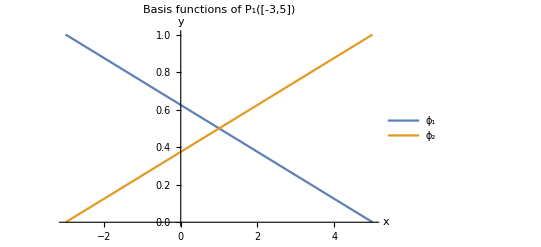

```mathematica
Subscript[ϕ, 1][r_]:=(Subscript[x, 2]-r)/(Subscript[x, 2]-Subscript[x, 1])
Subscript[ϕ, 2][r_]:=(r-Subscript[x, 1])/(Subscript[x, 2]-Subscript[x, 1])
Plot[Evaluate[{Subscript[ϕ, 1][r],Subscript[ϕ, 2][r]}/.{Subscript[x, 1]->-3,Subscript[x, 2]->5}],{r,-3,5},PlotLegends->{"ϕ_1","ϕ_2"},AxesLabel->{"x","y"},PlotLabel->"Basis functions of P_1([-3,5])"]
```

```mathematica
κ[x_]:=Subscript[κ, 1] Subscript[ϕ, 1][x]+Subscript[κ, 2] Subscript[ϕ, 2][x]
Subscript[g, D][x_]:=Subscript[g, Subscript[D, 1]] Subscript[ϕ, 1][x]+Subscript[g, Subscript[D, 2]] Subscript[ϕ, 2][x]
Subscript[g, N][x_]:=Subscript[g, Subscript[N, 1]] Subscript[ϕ, 1][x]+Subscript[g, Subscript[N, 2]] Subscript[ϕ, 2][x]
```

```mathematica
Subscript[R, loc]=Table[∫_Subscript[x, 1]^Subscript[x, 2] κ[t]Subscript[ϕ, i][t]Subscript[ϕ, j][t]ⅆt,{i,2},{j,2}];
```

```mathematica
Subscript[r, loc]=Table[∫_Subscript[x, 1]^Subscript[x, 2] (κ[t]Subscript[g, D][t]+Subscript[g, N][t])Subscript[ϕ, i][t]ⅆt,{i,2}];
```

```mathematica
MatrixForm@Subscript[R, loc]
MatrixForm@Subscript[r, loc]
```

(-1/12 (x_1-x_2) (3 κ_1+κ_2) | -1/12 (x_1-x_2) (κ_1+κ_2)
-1/12 (x_1-x_2) (κ_1+κ_2) | -1/12 (x_1-x_2) (κ_1+3 κ_2))

(-1/12 (x_1-x_2) (4 g_N_1+2 g_N_2+g_D_2 (κ_1+κ_2)+g_D_1 (3 κ_1+κ_2))
-1/12 (x_1-x_2) (2 g_N_1+4 g_N_2+g_D_1 (κ_1+κ_2)+g_D_2 (κ_1+3 κ_2)))

```mathematica
Assuming[n∈Integers&&m∈Integers&&n>0&&m>0,∫_Subscript[x, 1]^Subscript[x, 2] (Subscript[ϕ, 1][r])^n(Subscript[ϕ, 2][r])^m ⅆr]
```

ConditionalExpression[(m! n! (-x_1+x_2))/Gamma[2+m+n],x_1>0&&x_2>x_1]